```mathematica
f[v_, z_]:= -PolyLog[v, -z]
z[T_]:=FindRoot[4/(3 Sqrt[Pi] f[3/2,z])==T^(3/2),{z,Exp[1/T]}][[1,2]]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {6.0296931428×10^14172}. Try perturbing the initial point(s).

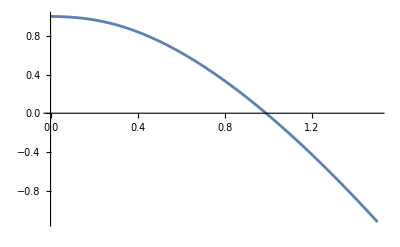

```mathematica
Plot[T*Log[z[T]], {T, 0, 1.5}]
```

```mathematica
Tratio[T_]:= (4/(3 Sqrt[Pi] f[3/2,z[T]]))^2/3
```

```mathematica
Unef[T_]:= 3/2 * Tratio[T] * (f[5/2, z[T]])/(f[3/2, z[T]])
```

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {1.4806172898×10^21259}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

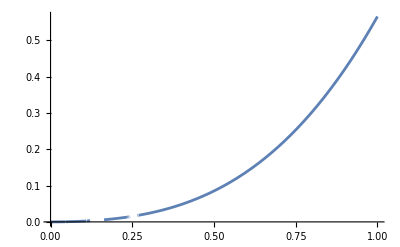

```mathematica
Plot[Unef[T], {T, 0, 1}]
```

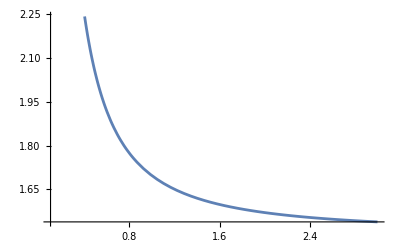

```mathematica
Plot[Unef[T]/Tratio[T], {T, 0.1, 3}]
SoverNk[T_]:= π^2 / (2Log[z[T]])
```

FindRoot::jsing: Encountered a singular Jacobian at the point {z} = {2.192227559×10^42518}. Try perturbing the initial point(s).

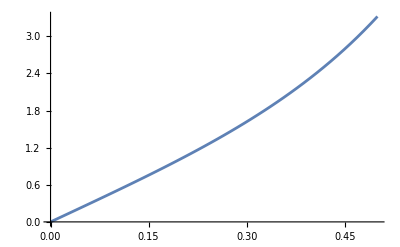

```mathematica
Plot[SoverNk[T], {T, 0, 0.5}]
```